## Uppgift 4

### Förklaring

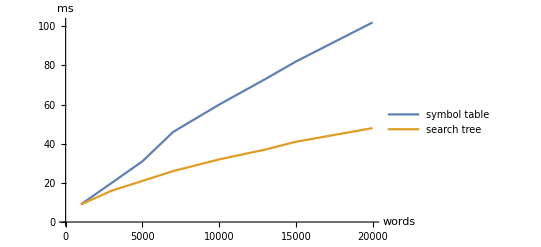

Vi ser att grafen för symbol table växer  linjärt i början, och verkar avta något mot ett logaritmiskt mönster för högre inläsningsstorlekar. 
Search tree verkar däremot växa logaritmiskt från början.

Skillnaden mellan algoritmerna är att när symbol table lägger in nya nycklar så har den en worst case av O(n) operationer, medan search tree
har en worst case på O(log n) operationer.  Det är inte omöjligt att symbol table övergår till ett logaritmiskt worst case för större inläsnings-
storlekar. Anledningen till detta kan vara att efter många ords lästs in, så blir det färre och färre fall av nya ord som inte än lagts in, och att
symbol table har en O(log n) för sökning av element som redan finns.

### Code

```mathematica
symbolTableTimes = {{1000,9},{3000,20},{5000,31},{7000,46},{10000,60},{13000,73},{15000,82},{20000,102}};
searchTreeTimes = {{1000,9},{3000,16},{5000,21},{7000,26},{10000,32},{13000,37},{15000,41},{20000,48}};
```

```mathematica
ListLinePlot[{symbolTableTimes,searchTreeTimes}, AxesLabel->{"words","ms"}, PlotLegends->{"symbol table","search tree"}];
```